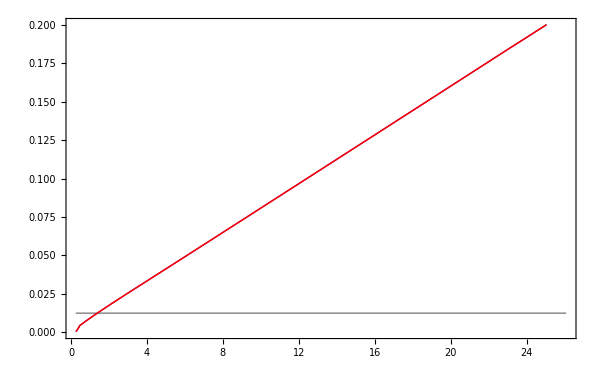

```mathematica
ClearAll["Global`*"]
wd=SetDirectory@NotebookDirectory[];

p1=Import[wd<>"/output/dt_adaptive.dat"];
t0=p1[[1,1]];
tf=p1[[-1,1]];
p1=Interpolation[p1,Method->"Spline"];
p2=Interpolation[Import[wd<>"/output/dt_CFL.dat"],Method->"Spline"];
p3=Interpolation[Import[wd<>"/output/dt_source.dat"],Method->"Spline"];

Plot[{0.0125,p3[t],p2[t],p1[t]},{t,t0,tf},PlotRange->{{t0,tf},{0.,0.2}},PlotStyle->{Gray,Purple,Blue,Red},Frame->True,Axes->None,ImageSize->600]
```